# Reconstruct zeta2, psi1, psi2 from zeta1

Given any solution y(x)=zeta1(x) of the fourth-order zeta1 ODE, this notebook derives zeta2, psi1, and psi2 directly from y and its derivatives. The important part is the algebraic elimination in Sections 3 and 4.

## 1. Setup

```mathematica
ClearAll["Global`*"];
$Assumptions = Element[{x, lam}, Reals] && x > 0 && lam > 0;

odeZeta1[y_] := x^2 D[y, {x, 4}] + 4 x (1 + I x) D[y, {x, 3}] +
   2 x (5 I - 2 x) D[y, {x, 2}] - 2 (I + 2 x) D[y, x] - lam^2 y;

(* Coefficients of the first-order system:
   zeta1' = A psi1 + B psi2
   zeta2' = C psi1 + D psi2
   psi1'  = E zeta1 + F zeta2
   psi2'  = G zeta1 + H zeta2 *)
coefA = I lam/(2 x^2) (I x - 1);
coefB = I lam/(2 x^2) (I x + 1) Exp[-2 I x];
coefC = I lam/(2 x^2) (I x - 1) Exp[2 I x];
coefD = I lam/(2 x^2) (I x + 1);
coefE = I lam/(2 x^2) (-(I x + 1));
coefF = I lam/(2 x^2) (I x + 1) Exp[-2 I x];
coefG = I lam/(2 x^2) (I x - 1) Exp[2 I x];
coefH = I lam/(2 x^2) (-(I x - 1));
```

## 2. Final reconstruction map

These are the formulas we want to derive. The next sections show how they are obtained from the first-order system.

```mathematica
psi1From[y_] := ((I x^2 + x) D[y, {x, 2}] + (-2 x^2 + 3 I x + 2) D[y, x])/(lam x);

psi2From[y_] := -I Exp[2 I x] ((x^2 + I x) D[y, {x, 2}] + (x + 2 I) D[y, x])/(lam x);

zeta2From[y_] := Exp[2 I x] (lam^2 y - 2 I x^2 D[y, {x, 3}] +
      4 x (x - I) D[y, {x, 2}] + 4 (x + I) D[y, x])/lam^2;
```

## 3. Algebraic derivation, step 1: differentiate zeta1 once

Set y0=y, y1=y', y2=y'', y3=y'''. We treat psi1, psi2, zeta2 as algebraic unknowns p1, p2, z2. The total derivative Dx uses the first-order system whenever p1, p2, or z2 are differentiated.

```mathematica
ClearAll[y0, y1, y2, y3, y4, p1, p2, z2];

p1Prime = coefE y0 + coefF z2;
p2Prime = coefG y0 + coefH z2;
z2Prime = coefC p1 + coefD p2;

Dx[expr_] := D[expr, x] + D[expr, y0] y1 + D[expr, y1] y2 +
   D[expr, y2] y3 + D[expr, y3] y4 +
   D[expr, p1] p1Prime + D[expr, p2] p2Prime + D[expr, z2] z2Prime;

rhs1 = coefA p1 + coefB p2;
eqFirst = y1 == rhs1;

rhs2 = FullSimplify[Dx[rhs1], Assumptions -> $Assumptions];
eqSecond = y2 == rhs2;

{eqFirst, eqSecond} // TraditionalForm
```

{y1==(ⅈ lam p1 (-1+ⅈ x))/(2 x^2)+(ⅈ lam p2 ⅇ^(-2 ⅈ x) (1+ⅈ x))/(2 x^2),y2==(lam ⅇ^(-2 ⅈ x) (p1 ⅇ^(2 ⅈ x) (x+2 ⅈ)+p2 ((3+2 ⅈ x) x-2 ⅈ)))/(2 x^3)}

A useful cancellation happens: after differentiating zeta1', the expression for y'' contains only psi1 and psi2, not zeta2. That is why the first two equations can solve for psi1 and psi2.

```mathematica
zeta2CoefficientInSecondDerivative = FullSimplify[Coefficient[Together[rhs2], z2], Assumptions -> $Assumptions]

psiSolutions = Solve[{eqFirst, eqSecond}, {p1, p2}] // FullSimplify;
psiSolutions // TraditionalForm

p1Formula = p1 /. First[psiSolutions];
p2Formula = p2 /. First[psiSolutions];

{p1Formula, p2Formula} // TraditionalForm
```

0

{{p1→((2+(-2 x+3 ⅈ) x) y1+(1+ⅈ x) x y2)/(lam x),p2→(ⅇ^(2 ⅈ x) ((2-ⅈ x) y1+(1-ⅈ x) x y2))/(lam x)}}

{((2+(-2 x+3 ⅈ) x) y1+(1+ⅈ x) x y2)/(lam x),(ⅇ^(2 ⅈ x) ((2-ⅈ x) y1+(1-ⅈ x) x y2))/(lam x)}

Thus psi1 and psi2 are already determined by y' and y''.

## 4. Algebraic derivation, step 2: differentiate one more time

Now differentiate y'' once more. This produces y''' and introduces zeta2 through psi1' and psi2'. Substituting the psi1 and psi2 formulas leaves one algebraic equation for zeta2.

```mathematica
rhs3BeforeSubstitution = FullSimplify[Dx[rhs2], Assumptions -> $Assumptions];

rhs3 = FullSimplify[rhs3BeforeSubstitution /. First[psiSolutions], Assumptions -> $Assumptions];
eqThird = y3 == rhs3;

zeta2Solution = Solve[eqThird, z2] // FullSimplify;
zeta2Solution // TraditionalForm

z2Formula = z2 /. First[zeta2Solution];
z2Formula // TraditionalForm
```

{{z2→(ⅇ^(2 ⅈ x) (lam^2 y0-2 ⅈ x^2 y3+4 (x+ⅈ) y1+4 x (x-ⅈ) y2))/lam^2}}

(ⅇ^(2 ⅈ x) (lam^2 y0-2 ⅈ x^2 y3+4 (x+ⅈ) y1+4 x (x-ⅈ) y2))/lam^2

This completes the elimination: {y',y''} gives psi1 and psi2, and y''' gives zeta2.

## 5. Convert the algebraic formulas into functions of y(x)

```mathematica
toFunctionRules = {
   y0 -> y[x],
   y1 -> D[y[x], x],
   y2 -> D[y[x], {x, 2}],
   y3 -> D[y[x], {x, 3}]
};

psi1Derived = FullSimplify[p1Formula /. toFunctionRules, Assumptions -> $Assumptions];
psi2Derived = FullSimplify[p2Formula /. toFunctionRules, Assumptions -> $Assumptions];
zeta2Derived = FullSimplify[z2Formula /. toFunctionRules, Assumptions -> $Assumptions];

{psi1Derived, psi2Derived, zeta2Derived} // TraditionalForm

checkAgainstDefinitions = FullSimplify[
   {psi1Derived - psi1From[y[x]], psi2Derived - psi2From[y[x]], zeta2Derived - zeta2From[y[x]]},
   Assumptions -> $Assumptions]
```

{((1+ⅈ x) x y''(x)+(2+(-2 x+3 ⅈ) x) y'(x))/(lam x),(ⅇ^(2 ⅈ x) ((1-ⅈ x) x y''(x)+(2-ⅈ x) y'(x)))/(lam x),(ⅇ^(2 ⅈ x) (lam^2 y(x)-2 ⅈ x^2 y^(3)(x)+4 x (x-ⅈ) y''(x)+4 (x+ⅈ) y'(x)))/lam^2}

{0,0,0}

Expected: checkAgainstDefinitions = {0,0,0}.

## 6. Direct verification of the original first-order system

The reconstructed functions satisfy three equations identically. The remaining zeta2 equation is proportional to the fourth-order zeta1 equation, so it vanishes whenever y solves the zeta1 ODE.

```mathematica
ClearAll[y];

z1 = y[x];
z2rec = zeta2From[z1];
p1rec = psi1From[z1];
p2rec = psi2From[z1];

resZeta1 = FullSimplify[D[z1, x] - (coefA p1rec + coefB p2rec), Assumptions -> $Assumptions]

resPsi1 = FullSimplify[D[p1rec, x] - (coefE z1 + coefF z2rec), Assumptions -> $Assumptions]

resPsi2 = FullSimplify[D[p2rec, x] - (coefG z1 + coefH z2rec), Assumptions -> $Assumptions]

resZeta2 = FullSimplify[D[z2rec, x] - (coefC p1rec + coefD p2rec), Assumptions -> $Assumptions]

zeta2ResidualCheck = FullSimplify[resZeta2 + 2 I Exp[2 I x] odeZeta1[z1]/lam^2, Assumptions -> $Assumptions]
```

0

0

0

(2 ⅇ^(2 ⅈ x) (ⅈ lam^2 y[x]+(-2+4 ⅈ x) y'[x]+x (2 (5+2 ⅈ x) y''[x]+4 (-ⅈ+x) y^(3)[x]-ⅈ x y^(4)[x])))/lam^2

0

Expected: resZeta1=0, resPsi1=0, resPsi2=0, and zeta2ResidualCheck=0. Equivalently, resZeta2=-(2 I Exp[2 I x]/lam^2) odeZeta1[y[x]].

## 7. Use with the zeta1 basis

After defining your four zeta1 basis functions, apply the reconstruction map to each one.

```mathematica
zeta1basis = {
(1-I*lam)LaguerreL[I*lam/2,-2*I*x]+I*lam*Hypergeometric1F1[1-I*lam/2,2,-2*I*x], 
(1+I*lam)LaguerreL[-I*lam/2,-2*I*x]-I*lam*Hypergeometric1F1[1+I*lam/2,2,-2*I*x],(1-I*lam)HypergeometricU[-I*lam/2,1,-2*I*x]-I*lam*HypergeometricU[1-I*lam/2,2,-2*I*x],
(1+I*lam)HypergeometricU[I*lam/2,1,-2*I*x]+I*lam*HypergeometricU[1+I*lam/2,2,-2*I*x]};
```

```mathematica
fullSystemBasis = FullSimplify[Table[
   {zeta1basis[[j]],
    zeta2From[zeta1basis[[j]]],
    psi1From[zeta1basis[[j]]],
    psi2From[zeta1basis[[j]]]},
   {j, Length[zeta1basis]}
],Assumptions->{x∈PositiveReals,lam∈PositiveReals}];
```

```mathematica
Bmat=fullSystemBasis;

cvec={c1,c2,c3,c4};

(*cvec.Bmat;*)
```

# Matching solutions for a rectangular function coupling

The four ’s solutions are

```mathematica
Bmat[[1]][[1]]
Bmat[[2]][[1]]
Bmat[[3]][[1]]
Bmat[[4]][[1]]
```

ⅈ lam Hypergeometric1F1[1-(ⅈ lam)/2,2,-2 ⅈ x]+(1-ⅈ lam) LaguerreL[(ⅈ lam)/2,-2 ⅈ x]

-ⅈ lam Hypergeometric1F1[1+(ⅈ lam)/2,2,-2 ⅈ x]+(1+ⅈ lam) LaguerreL[-(ⅈ lam)/2,-2 ⅈ x]

-ⅈ lam HypergeometricU[1-(ⅈ lam)/2,2,-2 ⅈ x]+(1-ⅈ lam) HypergeometricU[-(ⅈ lam)/2,1,-2 ⅈ x]

ⅈ lam HypergeometricU[1+(ⅈ lam)/2,2,-2 ⅈ x]+(1+ⅈ lam) HypergeometricU[(ⅈ lam)/2,1,-2 ⅈ x]

The four ’s solutions are

```mathematica
Bmat[[1]][[2]]
Bmat[[2]][[2]]
Bmat[[3]][[2]]
Bmat[[4]][[2]]
```

1/lam^2 ⅇ^(2 ⅈ x) (-(4 (ⅈ+lam) (-4 ⅈ+lam) (-2 ⅈ+lam+(4+lam (-ⅈ+lam)) x+2 lam x^2) Hypergeometric1F1[-1-(ⅈ lam)/2,2,-2 ⅈ x])/(-2 ⅈ+lam)+ⅈ lam (4+lam (-2 ⅈ+lam+4 x)) Hypergeometric1F1[1-(ⅈ lam)/2,2,-2 ⅈ x]+lam^2 (-2 ⅈ+lam) x Hypergeometric1F1[1-(ⅈ lam)/2,3,-2 ⅈ x]+((1-ⅈ lam) (32 (-ⅈ+x)+lam (16+lam^2+16 x (-ⅈ+x)+2 lam (-ⅈ+6 x))) LaguerreL[1+(ⅈ lam)/2,-2 ⅈ x])/(-2 ⅈ+lam))

1/lam^2 ⅇ^(2 ⅈ x) ((4 (4+lam (3 ⅈ+lam)) (-2 ⅈ+4 x+lam (-1+(ⅈ+lam-2 x) x)) Hypergeometric1F1[-1+(ⅈ lam)/2,2,-2 ⅈ x])/(2 ⅈ+lam)-ⅈ lam (4+lam (2 ⅈ+lam-4 x)) Hypergeometric1F1[1+(ⅈ lam)/2,2,-2 ⅈ x]-lam^2 (2 ⅈ+lam) x Hypergeometric1F1[1+(ⅈ lam)/2,3,-2 ⅈ x]+((1+ⅈ lam) (-32 (-ⅈ+x)+lam (16+lam^2+lam (2 ⅈ-12 x)+16 x (-ⅈ+x))) LaguerreL[1-(ⅈ lam)/2,-2 ⅈ x])/(2 ⅈ+lam))

-1/(16 x^3)ⅈ ⅇ^(2 ⅈ x) ((6 ⅈ+lam) (2 ⅈ+lam (ⅈ+lam) x) HypergeometricU[-(ⅈ lam)/2,-3,-2 ⅈ x]+2 (6+lam x (2-3 ⅈ lam+2 (ⅈ+lam) x)) HypergeometricU[-(ⅈ lam)/2,-2,-2 ⅈ x])

1/(16 x^3)ⅈ ⅇ^(2 ⅈ x) ((-6 ⅈ+lam) (2 ⅈ+lam (-ⅈ+lam) x) HypergeometricU[(ⅈ lam)/2,-3,-2 ⅈ x]+2 (-6+lam (2+lam (3 ⅈ-2 x)+2 ⅈ x) x) HypergeometricU[(ⅈ lam)/2,-2,-2 ⅈ x])

The four ’s solutions are

```mathematica
Bmat[[1]][[3]]
Bmat[[2]][[3]]
Bmat[[3]][[3]]
Bmat[[4]][[3]]
```

(-ⅈ+lam (-2+ⅈ/x-2 ⅈ x)+2 x) Hypergeometric1F1[1-(ⅈ lam)/2,2,-2 ⅈ x]+1/2 (2 ⅈ+lam) (ⅈ x+lam (-ⅈ+x)) Hypergeometric1F1[2-(ⅈ lam)/2,3,-2 ⅈ x]

1/(2 x)((2 (ⅈ-2 x) x+lam (2 ⅈ-4 x-4 ⅈ x^2)) Hypergeometric1F1[1+(ⅈ lam)/2,2,-2 ⅈ x]-(-2 ⅈ+lam) x (-ⅈ x+lam (-ⅈ+x)) Hypergeometric1F1[2+(ⅈ lam)/2,3,-2 ⅈ x])

2 (lam-x+ⅈ lam x) HypergeometricU[1-(ⅈ lam)/2,3,-2 ⅈ x]+((lam-x) HypergeometricU[-(ⅈ lam)/2,0,-2 ⅈ x])/(2 x^2)

2 (lam+x+ⅈ lam x) HypergeometricU[1+(ⅈ lam)/2,3,-2 ⅈ x]+((lam+x) HypergeometricU[(ⅈ lam)/2,0,-2 ⅈ x])/(2 x^2)

The four ’s solutions are

```mathematica
Bmat[[1]][[4]]
Bmat[[2]][[4]]
Bmat[[3]][[4]]
Bmat[[4]][[4]]
```

-1/(2 x)ⅇ^(2 ⅈ x) (2 ⅈ (-lam+x+2 ⅈ lam x+2 (-ⅈ+lam) x^2) Hypergeometric1F1[1-(ⅈ lam)/2,2,-2 ⅈ x]+(-2 ⅈ+lam) x (-ⅈ x+lam (ⅈ+x)) Hypergeometric1F1[1-(ⅈ lam)/2,3,-2 ⅈ x])

1/(2 x)ⅇ^(2 ⅈ x) ((2 x (ⅈ+2 x)+lam (2 ⅈ+4 x-4 ⅈ x^2)) Hypergeometric1F1[1+(ⅈ lam)/2,2,-2 ⅈ x]+(2 ⅈ+lam) x (ⅈ x+lam (ⅈ+x)) Hypergeometric1F1[1+(ⅈ lam)/2,3,-2 ⅈ x])

1/(8 x^3)ⅇ^(2 ⅈ x) ((4 ⅈ+lam) (lam-x) HypergeometricU[-(ⅈ lam)/2,-2,-2 ⅈ x]+2 (2 ⅈ x+lam^2 x (ⅈ+x)+ⅈ lam (-2+x^2)) HypergeometricU[-(ⅈ lam)/2,-1,-2 ⅈ x])

-1/(8 x^3)ⅇ^(2 ⅈ x) ((-4 ⅈ+lam) (lam+x) HypergeometricU[(ⅈ lam)/2,-2,-2 ⅈ x]+2 (2 ⅈ lam+ⅈ (2+lam^2) x+lam (-ⅈ+lam) x^2) HypergeometricU[(ⅈ lam)/2,-1,-2 ⅈ x])

Let’s compute the constant vector  by matching the in- and feature-regions’ solutions at , as

```mathematica
Vin1={1,0,0,0};
Vin2={0,0,1,0};

cvec1={c11,c12,c13,c14};
cvec2={c21,c22,c23,c24};

eqs1=Thread[(cvec1.(Bmat/. x->(k/H)*Exp[-N1]))==Vin1];
eqs2=Thread[(cvec2.(Bmat/. x->(k/H)*Exp[-N1]))==Vin2];

solC1=Solve[eqs1,cvec1][[1]];
solC2=Solve[eqs2,cvec2][[1]];
```

where the solutions are horrible, but exist.

Let’s save these results in advanced,

```mathematica
DumpSave["matchingResults.mx",{solC1,solC2,Bmat}];
```

and we can recover them directly using

```mathematica
Get["matchingResults.mx"]
```

Finally, the out-region solutions, for every , would be given by

```mathematica
Vin1={1,0,0,0};
Vin2={0,0,1,0};

cvec1={c11,c12,c13,c14};
cvec2={c21,c22,c23,c24};

Vout1=cvec1.(Bmat/. x->(k/H)*Exp[-N2]);

Vout2=cvec2.(Bmat/. x->(k/H)*Exp[-N2]);
```

and replacing with the values we found for the constant vectors

```mathematica
Vout1=Vout1/. solC1;

Vout2=Vout2/. solC2;
```

Saving this too

```mathematica
DumpSave["matchingResults.mx",{solC1,solC2,Bmat,Vout1,Vout2}];
```

## Power spectrum

Loading the results

```mathematica
Get["matchingResults.mx"];
```

We can do a quick check

```mathematica
N[(Vout1[[1]])/.{N1->1,N2->3,lam->1,H->1,k->2.5}]
```

0.852264+0.316486 ⅈ

Using Vout1 and Vou2 we can compute the power spectrum associated to both fields  and . The following cell provides a discrete plot of these quantities for specific values of

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-0.703998-2.02772 ⅈ,7.72998×10^6-6.81067×10^6 ⅈ,-8724.+24936.1 ⅈ,0.00210527+0.00434987 ⅈ},«2»,{1.93665+0.900587 ⅈ,-7.63925×10^6+7.0168×10^6 ⅈ,-2168.94-«1»,-0.00288112+0.000120339 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-0.583437-1.86217 ⅈ,5.24545×10^6-1.07349×10^7 ⅈ,-13098.+22907.5 ⅈ,0.00331121+0.00323857 ⅈ},{«1»},«1»,{1.78227+0.762733 ⅈ,-1.12775×10^7+4.16847×10^6 ⅈ,«18»-«18» ⅈ,-0.00215412-0.00132431 ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-0.703998-2.02772 ⅈ,7.72998×10^6-6.81067×10^6 ⅈ,-8724.+24936.1 ⅈ,0.00210527+0.00434987 ⅈ},«2»,{1.93665+0.900587 ⅈ,-7.63925×10^6+7.0168×10^6 ⅈ,-2168.94-«1»,-0.00288112+0.000120339 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-0.583437-1.86217 ⅈ,5.24545×10^6-1.07349×10^7 ⅈ,-13098.+22907.5 ⅈ,0.00331121+0.00323857 ⅈ},{«1»},«1»,{1.78227+0.762733 ⅈ,-1.12775×10^7+4.16847×10^6 ⅈ,«18»-«18» ⅈ,-0.00215412-0.00132431 ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

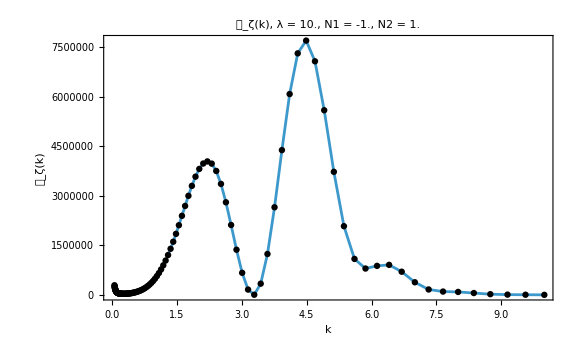

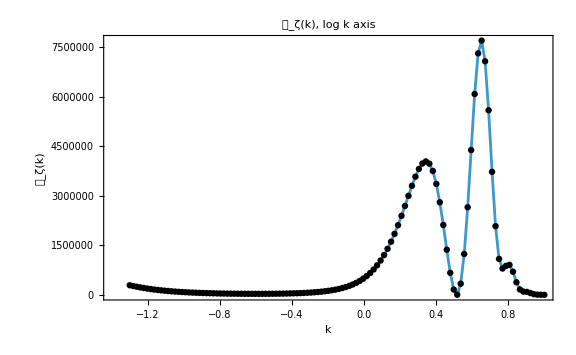

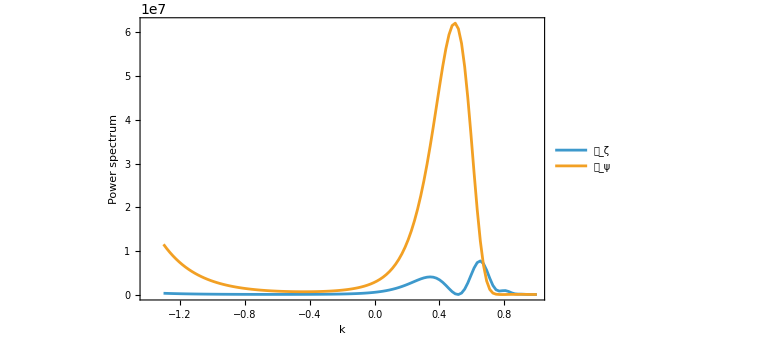

```mathematica
(* ============================================================*)(*Power spectrum from rectangular feature in e-folds N*)(*x(k,N)=Exp[Nk-N]=(k/H) Exp[-N]*)(*No Simplify/FullSimplify is used*)(* ============================================================*)Clear[xOfKN,x1OfK,x2OfK,lambdaSymbol,xSymbol,Vin1,Vin2,Vout1Numeric,Vout2Numeric,P0Numeric,PzetaNumeric,PpsiNumeric,kGridLinear,kGridLog,pZetaData,pPsiData,lamVal,HVal,epsVal,MplVal,N1Val,N2Val,kVal,wp,kMin,kMax,nPts];

(*Symbols used inside fullSystemBasis*)
lambdaSymbol=lam;
xSymbol=x;

(*Your basis matrix with row-vector convention:V^(i)(x)=c^(i).Bmat*)
(*Bmat=fullSystemBasis;*)

(*Initial quantum modes*)
Vin1={1,0,0,0};
Vin2={0,0,1,0};

(*E-fold expression for x*)
xOfKN[kval_?NumericQ,Hval_?NumericQ,Nval_?NumericQ]:=(kval/Hval) Exp[-Nval];

x1OfK[kval_?NumericQ,Hval_?NumericQ,N1val_?NumericQ]:=xOfKN[kval,Hval,N1val];

x2OfK[kval_?NumericQ,Hval_?NumericQ,N2val_?NumericQ]:=xOfKN[kval,Hval,N2val];

(*Out-region Bogoliubov vector for the first physical quantum mode*)
Vout1Numeric[lamval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ,kval_?NumericQ,Hval_?NumericQ,wpval_:40]:=Module[{x1val,x2val,B1,B2,c1},x1val=x1OfK[kval,Hval,N1val];
x2val=x2OfK[kval,Hval,N2val];
B1=N[Bmat/. {lambdaSymbol->lamval,xSymbol->x1val},wpval];
B2=N[Bmat/. {lambdaSymbol->lamval,xSymbol->x2val},wpval];
(*Row convention:c.B1==Vin1.Mathematica solves Transpose[B1].c==Vin1.*)c1=LinearSolve[Transpose[B1],Vin1];
Chop[c1.B2]]

(*Out-region Bogoliubov vector for the second physical quantum mode*)
Vout2Numeric[lamval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ,kval_?NumericQ,Hval_?NumericQ,wpval_:40]:=Module[{x1val,x2val,B1,B2,c2},x1val=x1OfK[kval,Hval,N1val];
x2val=x2OfK[kval,Hval,N2val];
B1=N[Bmat/. {lambdaSymbol->lamval,xSymbol->x1val},wpval];
B2=N[Bmat/. {lambdaSymbol->lamval,xSymbol->x2val},wpval];
c2=LinearSolve[Transpose[B1],Vin2];
Chop[c2.B2]]

(*Slow-roll normalization*)
P0Numeric[Hval_?NumericQ,epsval_?NumericQ,Mplval_?NumericQ]:=Hval^2/(8 Pi^2 epsval Mplval^2);

(*Curvature power spectrum*)
PzetaNumeric[lamval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ,kval_?NumericQ,Hval_?NumericQ,epsval_?NumericQ,Mplval_?NumericQ,wpval_:40]:=Module[{v1,v2,p0,result},v1=Vout1Numeric[lamval,N1val,N2val,kval,Hval,wpval];
v2=Vout2Numeric[lamval,N1val,N2val,kval,Hval,wpval];
p0=P0Numeric[Hval,epsval,Mplval];
result=p0 (Abs[v1[[1]]+v1[[2]]]^2+Abs[v2[[1]]+v2[[2]]]^2);
Re[Chop[result]]]

(*Optional:isocurvature power spectrum*)
PpsiNumeric[lamval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ,kval_?NumericQ,Hval_?NumericQ,epsval_?NumericQ,Mplval_?NumericQ,wpval_:40]:=Module[{v1,v2,p0,result},v1=Vout1Numeric[lamval,N1val,N2val,kval,Hval,wpval];
v2=Vout2Numeric[lamval,N1val,N2val,kval,Hval,wpval];
p0=P0Numeric[Hval,epsval,Mplval];
result=p0 (Abs[v1[[3]]+v1[[4]]]^2+Abs[v2[[3]]+v2[[4]]]^2);
Re[Chop[result]]]

(* ============================================================*)
(*Numerical sampling*)
(* ============================================================*)

(*Choose numerical parameters*)
lamVal=10.0;
HVal=1.0;
epsVal=0.01;
MplVal=1.0;

N1Val=-1.0;
N2Val=1.0;

wp=50;

(*Choose k-grid*)
kMin=0.05;
kMax=10;
nPts=120;

kGridLinear[kmin_,kmax_,n_]:=Subdivide[kmin,kmax,n-1];

kGridLog[kmin_,kmax_,n_]:=Exp[Subdivide[Log[kmin],Log[kmax],n-1]];

(*Use logarithmic grid if you want to resolve several decades in k*)
kValues=kGridLog[kMin,kMax,nPts];

(*Evaluate P_zeta(k) in advance*)
pZetaData=Table[{kval,PzetaNumeric[lamVal,N1Val,N2Val,kval,HVal,epsVal,MplVal,wp]},{kval,kValues}];

(*Optional:evaluate P_psi(k) too*)
pPsiData=Table[{kval,PpsiNumeric[lamVal,N1Val,N2Val,kval,HVal,epsVal,MplVal,wp]},{kval,kValues}];

(*Save numerical results*)
DumpSave["powerSpectrumData.mx",{pZetaData,pPsiData,lamVal,N1Val,N2Val,HVal,epsVal,MplVal}];

Export["PzetaData.csv",pZetaData];
Export["PpsiData.csv",pPsiData];

(* ============================================================*)
(*Discrete plots*)
(* ============================================================*)

ListLinePlot[pZetaData,Frame->True,PlotRange->All,Joined->True,Mesh->All,MeshStyle->Directive[Black,PointSize[0.008]],FrameLabel->{"k","\!\(\*SubscriptBox[\(𝒫\), \(ζ\)]\)(k)"},PlotLabel->Row[{"\!\(\*SubscriptBox[\(𝒫\), \(ζ\)]\)(k),  ","λ = ",lamVal,",  N1 = ",N1Val,",  N2 = ",N2Val}],ImageSize->Large]

(*Optional log-k plot*)
ListLinePlot[pZetaData,Frame->True,PlotRange->All,Joined->True,ScalingFunctions->{"Log10",None},Mesh->All,MeshStyle->Directive[Black,PointSize[0.008]],FrameLabel->{"k","\!\(\*SubscriptBox[\(𝒫\), \(ζ\)]\)(k)"},PlotLabel->Row[{"\!\(\*SubscriptBox[\(𝒫\), \(ζ\)]\)(k), log k axis"}],ImageSize->Large]

(*Optional:compare curvature and isocurvature spectra*)
ListLinePlot[{pZetaData,pPsiData},Frame->True,PlotRange->All,Joined->True,ScalingFunctions->{"Log10",None},FrameLabel->{"k","Power spectrum"},PlotLegends->Placed[{"\!\(\*SubscriptBox[\(𝒫\), \(ζ\)]\)","\!\(\*SubscriptBox[\(𝒫\), \(ψ\)]\)"},Right],ImageSize->Large]
```